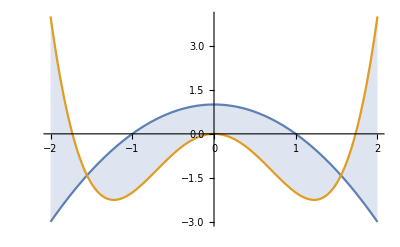

```mathematica
f[x_]=1-x^2;
g[x_]=x^4-3 x^2;
Plot[{f[x],g[x]},{x,-2,2},Filling->{1->{2}}]
```

```mathematica
intersectionpoints=Solve[f[x]==g[x]]
```

{{x→-ⅈ √(-1+√2)},{x→ⅈ √(-1+√2)},{x→-√(1+√2)},{x→√(1+√2)}}

```mathematica
a=intersectionpoints[[3,1,2]];
b=intersectionpoints[[4,1,2]];
Integrate[f[x]-g[x],{x,a,b}]//N
```

4.48665

```mathematica
(*The required area is 4.48665 square units*)
```